```mathematica
(* Different approach: suppose δ is piecewise affine continuous *)
time = {0,10, 100,500};

(* Transition probabilities starting with p[0] = 1 *)
s = {1,0.50,0.95,0.99};
δInit := 0.0020;

(* Define δ from proba transitions *)
Clear[δ];
For[i=1, i<= Length[time]-1,i++, δ[i]=a[i]+b[i]*t];
δ[Length[time]] = - Log[s [[Length[time]]]];


(* Compute δ coefficients *)
sol[Length[time]] = {a[Length[time]] ->-Log[s[[Length[time]]]],b[Length[time]] -> 0};
For[i=2, i<= Length[time]-1, i++, sol[i]= nSolve[{a[i]+b[i]* time[[i+1]] == -Log[s[[i+1]]],a[i]+b[i]*time[[i]]== -Log[s[[i]]] },{a[i],b[i]}]];
sol[1]=Solve[a[1]+b[1]* time[[2]]==-Log[s[[2]]]&& a[1]+b[1]* time[[1]]== δInit, {a[1], b[1]}];
For[i=1, i<= Length[time], i++,Print[sol[i]]]
```

{{a[1]→0.002,b[1]→0.0691147}}

{{a[2]→0.764464,b[2]→-0.00713171}}

{{a[3]→0.061604,b[3]→-0.000103107}}

{a[4]→0.0100503,b[4]→0}

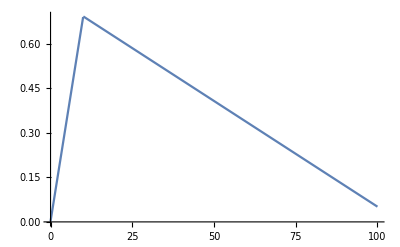

```mathematica
(* Define δ as piecewise and plot δ *)
Clear[δ]
For[i=1, i<= Length[time],i++, δ[i]=a[i]+b[i]*t/.sol[i]];
δGraph = ConstantArray[t,{Length[time]-1,2 }];
For[i=1, i<=Length[time]-1,i++,δGraph[[i]][[1]] = δ[i][[1]]; δGraph[[i]][[2]]= time[[i]]<=t<=time[[i+1]]];
δPiece= Piecewise[δGraph, δ[Length[time]]];
Plot[δPiece,{t,0,100}]
```

```mathematica
(* Solve TPR model *)
(* Define Hamiltonian of reducing AI risks (note that variable p stands for probability of survival) *)
H = p* x^{1-η}/(1-η)δX+ v(r*m-x+Subscript[ϕ, o] B(δS/δInit)^γ)+ w*p;
D[H,m]
```

{r v}

```mathematica
(* Derive optimal spending schedule expression  *)
Clear[xStar]
xSol = SolveValues[D[H,x]==0,x ];
(* Solve diff equation on conjuguate of m *)
vStar= DSolveValue[v'[t]==-r *v[t],v[t], t];
(* Opitmal spending schedule *)
δInt = Integrate[δPiece/.t->τ,{τ,0,t},Assumptions->0<=t]//FullSimplify ;
xStar = xSol/.{δS -> δPiece,v-> vStar, p -> Exp[-δInt]}
xStar
```

SolveValues::ifun: Inverse functions are being used by SolveValues, so some solutions may not be found; use Reduce for complete solution information.

{((ⅇ^(-r t+(Piecewise[{{0., t≤0}, {44.2191+0.0100503 t, t>500.}, {(0.002+0.0345574 t) t, 0<t≤10.}, {31.3307+(0.061604-0.0000515537 t) t, 100.<t≤500.}, {-3.81232+(0.764464-0.00356585 t) t, True}}])) C[1])/Piecewise[{{0.002+0.0691147 t, 0≤t≤10}, {0.764464-0.00713171 t, 10≤t≤100}, {0.061604-0.000103107 t, 100≤t≤500}, {0.0100503, True}}])^(-1/η)}

{((ⅇ^(-r t+(Piecewise[{{0., t≤0}, {44.2191+0.0100503 t, t>500.}, {(0.002+0.0345574 t) t, 0<t≤10.}, {31.3307+(0.061604-0.0000515537 t) t, 100.<t≤500.}, {-3.81232+(0.764464-0.00356585 t) t, True}}])) C[1])/Piecewise[{{0.002+0.0691147 t, 0≤t≤10}, {0.764464-0.00713171 t, 10≤t≤100}, {0.061604-0.000103107 t, 100≤t≤500}, {0.0100503, True}}])^(-1/η)}

```mathematica
xStar[[1]]
```

((ⅇ^(-r t+(Piecewise[{{0., t≤0}, {44.2191+0.0100503 t, t>500.}, {(0.002+0.0345574 t) t, 0<t≤10.}, {31.3307+(0.061604-0.0000515537 t) t, 100.<t≤500.}, {-3.81232+(0.764464-0.00356585 t) t, True}}])) C[1])/Piecewise[{{0.002+0.0691147 t, 0≤t≤10}, {0.764464-0.00713171 t, 10≤t≤100}, {0.061604-0.000103107 t, 100≤t≤500}, {0.0100503, True}}])^(-1/η)

```mathematica
parametersEval = {  r->0.05,ϕ->0,B->100,γ->5,η->2}
```

{r→0.05,ϕ→0,B→100,γ→5,η→2}

```mathematica
(* Derive C[1] using transversality condition. For last interval we neglect future funders and use δ constant *)
c = (-r+δ[Length[time]]+r η)^-η (B/η)^-η/.parametersEval
```

0.110925

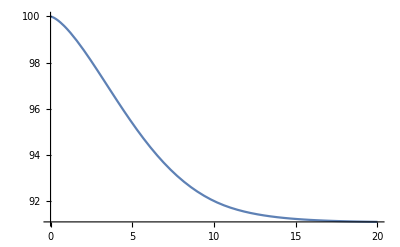

```mathematica
(* numerically solve differential equation on money available *)
evalSol = nDSolveValue[{m'[t]== r*m[t]- xStar[[1]]+ϕ*B(δPiece/δInit)^γ, m[0]==B}/.parametersEval/.C[1]->c  ,m[t],{t,0,20}];

(* Plot solution *)
Plot[(m[t]*Exp[-r * t])/.m[t]->evalSol/.parametersEval, {t,0,20}]
```

```mathematica
m[t]/.m[t]->evalSol
```

InterpolatingFunction[…][t]

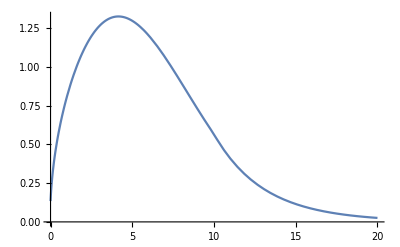

```mathematica
(* Plot spending schedule *)
Plot[xStar/. parametersEval/.C[1]->c, {t,0,20}]
```

```mathematica
parametersEval = {r->0.05,ϕ->0.10,B->100,δInit->0.0020,γ->5,η->2,b->1, a->1,C[1]->c, t0 -> 0};
Plot[m[t]/.(m[t]-> mStar)/.parametersEval,{t, 2021,2100}]
```

```mathematica
(* Include non AI risks *)
fBio = kBio * xBio^(1- ηBio)/(1 - ηBio);
fOther = kOther * xOther^(1 - ηOther)/(1 - ηOther);
sBio = {1, 0.90, 0.99, 0.995};
sOther = {1, 0.95, 0.99, 0.995};
```

```mathematica
(* Define function to compute delta *)
fDelta[s0_, δ0_, time0_, δInit0_]:= Module[{s = s0, time=time0, δInit=δInit0}, 
(* Define delta *)
For[i=1, i<= Length[time]-1,i++, δ[i]=a[i]+b[i]*t  ];δ[Length[time]] = - Log[s [[Length[time]]]];
sol[Length[time]] = {a[Length[time]] ->-Log[s[[Length[time]]]],b[Length[time]] -> 0};

(* Compute coefficients *)
For[i=2, i<= Length[time]-1, i++, sol[i]= nSolve[{a[i]+b[i]* time[[i+1]] == -Log[s[[i+1]]],a[i]+b[i]*time[[i]]== -Log[s[[i]]] },{a[i],b[i]}]];
sol[1]=Solve[a[1]+b[1]* time[[2]]==-Log[s[[2]]]&& a[1]+b[1]* time[[1]]== δInit, {a[1], b[1]}];
For[i=1, i<= Length[time], i++,Print[sol[i]]]

(* Replace coefficients in delta *)
For[i=1, i<= Length[time],i++, δ[i]=a[i]+b[i]*t/.sol[i]];

(* Define piecewise affine graph *)
δGraph = ConstantArray[t,{Length[time]-1,2 }];
For[i=1, i<=Length[time]-1,i++,δGraph[[i]][[1]] = δ[i][[1]]; δGraph[[i]][[2]]= time[[i]]<=t<=time[[i+1]]];

(* Return delta, unclear why this does not return deltaX *)
 δPiece= Piecewise[δGraph, δ[Length[time]]]]
```

```mathematica
time = {0,10, 100,500};
(* Transition probabilities starting with p[0] = 1 *)
s = {1,0.50,0.90,0.99};
δInit := 0.0020;
fDelta[s, time, δInit];
δA = Piecewise[δGraph, δ[Length[time]]]
Plot[δPiece, {t,0,100}]
```

Piecewise[{{0.002+0.0691147 t, 0≤t≤10}, {0.764464-0.00713171 t, 10≤t≤100}, {0.061604-0.000103107 t, 100≤t≤500}, {0.0100503, True}}]

-Graphics-

δGraph

```mathematica
fDelta[sBio, time, δInit];
δB= Piecewise[δGraph, δ[Length[time]]]
Plot[δB, {t,0,100}]
```

Piecewise[{{0.002+0.0691147 t, 0≤t≤10}, {0.764464-0.00713171 t, 10≤t≤100}, {0.061604-0.000103107 t, 100≤t≤500}, {0.0100503, True}}]

-Graphics-

{{a[1]→0.002,b[1]→0.00492933}}

{{a[2]→0.0558758,b[2]→-0.000458255}}

{{a[3]→0.0113098,b[3]→-0.0000125945}}

{a[4]→0.00501254,b[4]→0}

Piecewise[{{0.002+0.00492933 t, 0≤t≤10}, {0.0558758-0.000458255 t, 10≤t≤100}, {0.0113098-0.0000125945 t, 100≤t≤500}, {0.00501254, True}}]

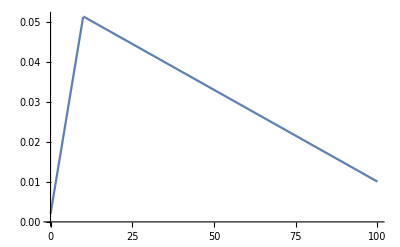

```mathematica
fDelta[sOther, time, δInit];
δO= Piecewise[δGraph, δ[Length[time]]]
Plot[δO, {t,0,100}]
```

```mathematica
(* Define hamiltonian: problem cannot integrate because of x[t] *)
H =p* (xAI^{1-ηAI}/(1-ηAI)δAI+ xBio^{1-ηBio}/(1-ηBio)δBio + xOther^{1-ηOther}/(1-ηOther)δOther) + v(r*m-(xAI +xBio + xOther)+Subscript[ϕ, o] B(δS/δInit)^γ)+ w*p;
```

```mathematica
H
```

{p w+p ((xAI^(1-ηAI) δAI)/(1-ηAI)+(xBio^(1-ηBio) δBio)/(1-ηBio)+(xOther^(1-ηOther) δOther)/(1-ηOther))+v (m r-xAI-xBio-xOther+500.^γ B δS^γ ϕ_o)}

```mathematica
xStarAI=SolveValues[D[H, xAI]==0, xAI]
xStarBio=SolveValues[D[H, xBio]==0, xBio]
xStarOther=SolveValues[D[H, xOther]==0, xOther]
```

SolveValues::ifun: Inverse functions are being used by SolveValues, so some solutions may not be found; use Reduce for complete solution information.

{(v/(p δAI))^(-1/ηAI)}

SolveValues::ifun: Inverse functions are being used by SolveValues, so some solutions may not be found; use Reduce for complete solution information.

{(v/(p δBio))^(-1/ηBio)}

SolveValues::ifun: Inverse functions are being used by SolveValues, so some solutions may not be found; use Reduce for complete solution information.

{(v/(p δOther))^(-1/ηOther)}

```mathematica
D[H,m]
vStar = DSolveValue[v'[t] == -r*v[t],v[t],t]
```

```mathematica
Clear[v'[t]]
```

Clear::ssym: v'[t] is not a symbol or a string.

Integrate::ilim: Invalid integration variable or limit(s) in Assumptions→0≤t.

```mathematica
(* Model considering only AI risks *)
H = p*x^(1-η)/(1- η)*s*δ+v*(r*m-x+ϕ)+w*p;
pDot = -δ*p;
sDot = (g-d)*s+b*x^ϵ+k*(x*s)^α;
mDot = r*m-x+ϕ;
ϕ=ϕInit*B*(δ/δInit)^γ;
```

```mathematica
(* Hamilton equations *)
xStar = SolveValues[D[H,x]==0, x];
vStar = DSolveValue[v'[t]==-r*v[t], v[t], t];
xStar = xStar/.(v->vStar)
```

SolveValues::ifun: Inverse functions are being used by SolveValues, so some solutions may not be found; use Reduce for complete solution information.

{((ⅇ^(-r t) C[1])/(p s δ))^(-1/η)}

```mathematica
(* Optimal money available *)
mDot = mDot/.(x->xStar);
sDot = sDot/.(x->xStar)
```

{(-d+g) s+b (((ⅇ^(-r t) C[1])/(p s δ))^(-1/η))^ϵ+k (s ((ⅇ^(-r t) C[1])/(p s δ))^(-1/η))^α}

```mathematica
(* Define delta *)
time = {0,10, 100,500};

(* Transition probabilities starting with p[0] = 1 *)
pTrans = {1,0.50,0.95,0.99};
δInit := 0.0020;

(* Define δ from proba transitions *)
Clear[δ];
For[i=1, i<= Length[time]-1,i++, δ[i]=a[i]+b[i]*t];
δ[Length[time]] = - Log[pTrans [[Length[time]]]];

(* Compute δ coefficients *)
sol[Length[time]] = {a[Length[time]] ->-Log[pTrans[[Length[time]]]],b[Length[time]] -> 0};
For[i=2, i<= Length[time]-1, i++, sol[i]= nSolve[{a[i]+b[i]* time[[i+1]] == -Log[pTrans[[i+1]]],a[i]+b[i]*time[[i]]== -Log[pTrans[[i]]] },{a[i],b[i]}]];
sol[1]=Solve[a[1]+b[1]* time[[2]]==-Log[pTrans[[2]]]&& a[1]+b[1]* time[[1]]== δInit, {a[1], b[1]}];
For[i=1, i<= Length[time], i++,Print[sol[i]]]

(* Define δ as piecewise, plot δ and integrate *)
Clear[δ]
For[i=1, i<= Length[time],i++, δ[i]=a[i]+b[i]*t/.sol[i]];
δGraph = ConstantArray[t,{Length[time]-1,2 }];
For[i=1, i<=Length[time]-1,i++,δGraph[[i]][[1]] = δ[i][[1]]; δGraph[[i]][[2]]= time[[i]]<=t<=time[[i+1]]];
δPiece= Piecewise[δGraph, δ[Length[time]]];
Plot[δPiece,{t,0,100}]
δInt = Integrate[δPiece/.t->τ,{τ,0,t},Assumptions->0<=t]//FullSimplify ;
```

{{a[1]→0.002,b[1]→0.0691147}}

{{a[2]→0.764464,b[2]→-0.00713171}}

{{a[3]→0.061604,b[3]→-0.000103107}}

{a[4]→0.0100503,b[4]→0}

-Graphics-

```mathematica
(* Express sDot in parameters *)
sDot = sDot/.{δ-> δPiece, p -> Exp[-δInt]}
```

{(-d+g) s+b (((ⅇ^(-r t+(Piecewise[{{0., t≤0}, {44.2191+0.0100503 t, t>500.}, {(0.002+0.0345574 t) t, 0<t≤10.}, {31.3307+(0.061604-0.0000515537 t) t, 100.<t≤500.}, {-3.81232+(0.764464-0.00356585 t) t, True}}])) C[1])/(s (Piecewise[{{0.002+0.0691147 t, 0≤t≤10}, {0.764464-0.00713171 t, 10≤t≤100}, {0.061604-0.000103107 t, 100≤t≤500}, {0.0100503, True}}])))^(-1/η))^ϵ+k (s ((ⅇ^(-r t+(Piecewise[{{0., t≤0}, {44.2191+0.0100503 t, t>500.}, {(0.002+0.0345574 t) t, 0<t≤10.}, {31.3307+(0.061604-0.0000515537 t) t, 100.<t≤500.}, {-3.81232+(0.764464-0.00356585 t) t, True}}])) C[1])/(s (Piecewise[{{0.002+0.0691147 t, 0≤t≤10}, {0.764464-0.00713171 t, 10≤t≤100}, {0.061604-0.000103107 t, 100≤t≤500}, {0.0100503, True}}])))^(-1/η))^α}

```mathematica
(* Define parameters *)
parameters = {d->0.5, g->0.6, k->1,b->1, ϵ->0.7, α->0.5,  r->0.05,ϕ->0,B->100,γ->5,η->2}
sStar = DSolveValue[s'[t]==(sDot[[1]]/.(s->s[t]))/.parameters, s[t],t]
```

```mathematica
{d->0.5,g->0.6,k->1,b->1,ϵ->0.7,α->0.5,r->0.05,500.^γ B δ^γ ϕInit->0,B->100,γ->5,η->2}
```

$Aborted

```mathematica
(* User input: define transition probabilities of survivial *)
time = {0,10,50,100};
sTrans = {0.70, 0.80, 0.90};
δInit := 0.0020;
δF :=0.0001;

(* Suppose δ is piecewise affine*)
For[i=1, i<= Length[time]-1,i++,
	δ[i]= a[i]+b[i]*t;   δInt[i]=Integrate[δ[i], {t, time[[i]],time[[i+1]]}];
];
δ[Length[time]]= δF;
δ[1]=δInit+b[1]*t;
```

```mathematica
(* Boundary conditions *)
n= Length[time];
sol[n]={{a[Length[time]] ->δF,b[Length[time]] -> 0}};
For[i=1, i<= n-1, i++, sol[n-i]= NSolve[{(δ[n-i]/.t->time[[n-i+1]])== (δ[n-i+1]/.t->time[[n-i+1]]/.sol[n-i+1]), δInt[n-i]== -Log[sTrans[[n-i]]]},{a[n-i],b[n-i]}];
];
```

```mathematica
(* Define δ as piecewise and plot δ *)
For[i=1, i<= Length[time],i++, δ[i]=δ[i]/.sol[i]];
δGraph = ConstantArray[t,{Length[time]-1,2 }];
For[i=1, i<=Length[time]-1,i++,δGraph[[i]][[1]] = δ[i][[1]]; δGraph[[i]][[2]]= time[[i]]<=t<=time[[i+1]]];
δPiece= Piecewise[δGraph, δ[Length[time]][[1]]];
```

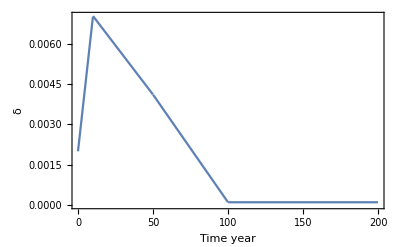

```mathematica
(* Plot δ *)
Plot[δPiece,{t,0,200}, Frame->True, FrameLabel->{Time (year), δ}]
```

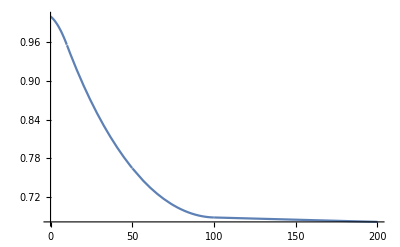

```mathematica
(* Plot probability of survival *)
δInt = Integrate[δPiece/.t->τ,{τ,0,t},Assumptions->0<=t]//FullSimplify ;
pS = Exp[-δInt];
Plot[pS, {t,0,200}]
```